# Plane-strain Arc Crack

```mathematica
PacletDirectoryLoad[NotebookDirectory[]<>"../../../../"]
<<BigWhamLink`
$BigWhamVersion
GetFilesDate[]
```

{/Users/bricelecampion/Documents/Work/Geomechanics/Codes/Pear/BigWhamLink/}

1.2.1

{/Users/bricelecampion/Documents/Work/Geomechanics/Codes/Pear/BigWhamLink/BigWhamLink/Kernel/../LibraryResources/MacOSX-x86-64/HmatExpressions.dylib→Mon 15 Mar 2021 16:41:45GMT+1,/Users/bricelecampion/Documents/Work/Geomechanics/Codes/BigWham/cmake-build-release/libBigWham.a→Mon 15 Mar 2021 16:39:37GMT+1}

## Reference solution

A . Piva . A crack along a circular interface between dissimilar media . Meccanica, 17 (2) : 85–90, jun 1982.

```mathematica
Wref[ϕ_,θ_]=-4 √2 Re[(ⅇ^(-1/2 ⅈ (2 θ+ϕ)) (-ⅇ^(ⅈ θ)+ⅇ^(ⅈ ϕ)) (-1+ⅇ^(ⅈ (θ+ϕ))) Pnet R √(1/(-Cos[θ]+Cos[ϕ])))/(Ep (-3+Cos[θ]))];
Vref[ϕ_,θ_]=-4 √2 Im[(ⅇ^(-1/2 ⅈ (2 θ+ϕ)) (-ⅇ^(ⅈ θ)+ⅇ^(ⅈ ϕ)) (-1+ⅇ^(ⅈ (θ+ϕ))) Pnet R √(1/(-Cos[θ]+Cos[ϕ])))/(Ep (-3+Cos[θ]))];
KIref[θ_]=(Pnet √(π R Sin[θ]))/(1+Sin[θ/2]^2)Cos[θ/2];
KIIref[θ_]=Abs[(Pnet √(π R Sin[θ]))/(1+Sin[θ/2]^2)Sin[θ/2]];
xtip1[θ_]=R Cos[-θ];
ytip1[θ_]=R Sin[-θ];
```

## Mesh

```mathematica
ArcCrackMesh[R_,α_,Nb_:10,RefTipRatio_:0.5,RefRatio_:1]:=Module[{coor,conn,Ne,Angle,Angle1,Angle2,Angle3,Nbc,Nbt
},
(* Default Value such that mesh is unifom *)
 (* RefRatio: Refinement ratio = (channel element size) / (tip element size) *)
 (* RefTipRatio ratio of refined tip to crack length, e.g. ==0.2 for 20% tip refined *)
(* Nb Number of Elements per fracture to get base mesh size away from tips *)

Nbc=Round[Nb*(1-2*RefTipRatio)]; 

(* Number of Elements per fracture in the unrefined "channel" away from tips, for 2 crack tips per fracture *)
Nbt=Round[RefRatio*Nb*RefTipRatio]; (* Number of Elements per fracture in the refined tips, for each crack tip *)
  
Angle1 = Table[ -α+(2 α*RefTipRatio/Nbt) i  ,{i,0,Nbt}];
Angle3 = Table[ α-(2 α*RefTipRatio/Nbt) i  ,{i,Nbt,0,-1}];
Angle2 = Table[Angle1[[-1]] +(2 α*(1-2*RefTipRatio)/Nbc) i  ,{i,1,Nbc-1}];
Angle=Join[Angle1,Angle2,Angle3];

(* = Nbc+2*Nbt = Total Number of Elements per fracture, for 2 crack tips per fracture *)
coor= Transpose[{R Cos[Angle],R Sin[Angle]}]//DeleteDuplicates;
Ne=Length[coor]-1;
conn =Table[{i,i+1},{i,1,Ne}]; 

<|"Coordinates"-> coor,"Connectivity"-> conn,"Nelts"-> Ne|>

]
```

## 2DP1 kernel

```mathematica
R=1.;
α=145/180*π;
```

```mathematica
mesh=ArcCrackMesh[R,α,20,0.5,3];
```

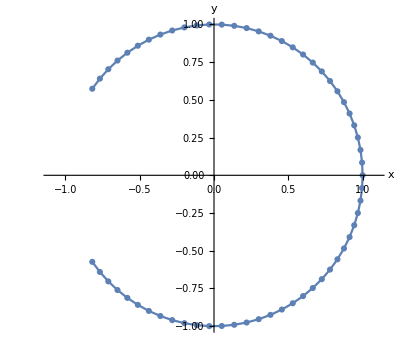

```mathematica
ListPlot[mesh["Coordinates"], PlotMarkers->Automatic,AxesLabel->{"x","y"},AspectRatio->Automatic,Joined->True,PlotRange->{{-1.1,1.1},All}]
```

```mathematica
Rock=<|"Young"-> 2.4,"Poisson"-> 0.2|>;
Ep=Rock["Young"]/(1-Rock["Poisson"]^2);
```

```mathematica
ker="2DP1"; 
ml=100; (* max leaf size - 100 is a good start *)
eta=3;  (* eta  - 3 is a good start (0 for no compression) *)
eps=0.001;  (* no 0.001 *)
prop={Rock["Young"],Rock["Poisson"]}; (* E, ν *) 
h1=toHMatExpr[mesh["Coordinates"],mesh["Connectivity"],ker,prop,ml,eta,eps];
```

constructor called

Now setting up and constructing the HMatrix ...

HMatrix is now set !

```mathematica
s=GetFullBlocks[h1]
```

SparseArray[…]

```mathematica
(* Unit Isotropic tensile loading *)
Pnet=1.;
LoadP1=ConstantArray[0., 4 Length[mesh["Connectivity"]]];
LoadP1[[2;;-1;;2]]=Pnet;
```

```mathematica
(* Solution via iterative Solve *)
fdot[x_?(VectorQ[#,NumericQ]&)]:=Hdot[h1,x];
{sol,stats}=Reap@LinearSolve[fdot,LoadP1,Method->{"Krylov",{"Method"->"BiCGSTAB"(*"GMRES"*)(*"BiCGSTAB"*),(*"Preconditioner"->precJ,"PreconditionerSide"->Right,*)(*"StartingVector"->v0,*)"Tolerance"->10^-6.,"MaxIterations"->1000,"ResidualNormFunction"->((Sow[Norm[#,2]])&)}}];
ds=sol[[1;;-1;;2]];dn=sol[[2;;-1;;2]];


(* Compare with ref solution  - get double vertex  *)
vertex = Flatten[mesh["Coordinates"][[#]] & /@ mesh["Connectivity"]  ,1];
thets= ArcTan[#[[1]],#[[2]] ] & /@ vertex;
 dsref=Vref[#,α]& /@ thets[[2;;-2]];
dnref=Wref[#,α]& /@ thets[[2;;-2]];
```

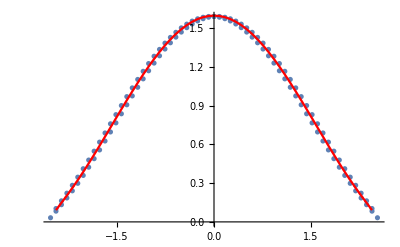

```mathematica
Show[ListPlot[ Transpose[{thets,dn}]],ListPlot[Transpose[{thets[[2;;-2]],dnref}],PlotStyle->Red,Joined->True]]
```

```mathematica
relerrDn=(Abs[(dn[[2;;-2]]-dnref)/dnref]);
relerrDs=(Abs[(ds[[2;;-2]]-dsref)/dsref]);
abserrDs=Abs[(ds[[2;;-2]]-dsref)];
abserrDn=Abs[(dn[[2;;-2]]-dnref)];
```

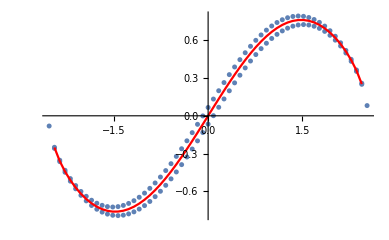

```mathematica
Show[ListPlot[ Transpose[{thets,ds}]],ListPlot[Transpose[{thets[[2;;-2]],dsref}],PlotStyle->Red,Joined->True]]
```

```mathematica
hx=Norm[vertex[[2]]-vertex[[1]]];
relK1=Abs[1-(dn[[2]]/(√(32./π) (1/Ep)  hx^(1/2)))/KIref[α]]
relK2=Abs[1-(Abs[ds[[2]]]/(√(32./π) (1/Ep)  hx^(1/2)))/KIIref[α]]
```

0.0606645

0.0410313

```mathematica
relerrDn //Median
relerrDs //Median
```

0.0296405

0.0568051

## 2DP0 kernel

```mathematica
R=1.;
α=145/180*π;
```

```mathematica
mesh=ArcCrackMesh[R,α,40,0.5,3];
```

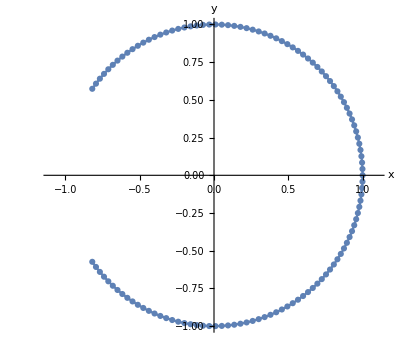

```mathematica
ListPlot[mesh["Coordinates"], PlotMarkers->Automatic,AxesLabel->{"x","y"},AspectRatio->Automatic,Joined->True,PlotRange->{{-1.1,1.1},All}]
```

```mathematica
Rock=<|"Young"-> 2.4,"Poisson"-> 0.2|>;
Ep=Rock["Young"]/(1-Rock["Poisson"]^2);
```

```mathematica
ker="S3DP0"; 
ml=100; (* max leaf size - 100 is a good start *)
eta=3;  (* eta  - 3 is a good start (0 for no compression) *)
eps=0.001;  (* no 0.001 *)
prop={Rock["Young"],Rock["Poisson"],10000.}; (* E, ν *) 
h1=toHMatExpr[mesh["Coordinates"],mesh["Connectivity"],ker,prop,ml,eta,eps];
```

constructor called

Now setting up and constructing the HMatrix ...

HMatrix is now set !

```mathematica
(* Unit Isotropic tensile loading *)
Pnet=1.;
LoadP1=ConstantArray[0., 2 Length[mesh["Connectivity"]]];
LoadP1[[2;;-1;;2]]=Pnet;
```

```mathematica
(* Solution via iterative Solve *)
fdot[x_?(VectorQ[#,NumericQ]&)]:=Hdot[h1,x];
{sol,stats}=Reap@LinearSolve[fdot,LoadP1,Method->{"Krylov",{"Method"->"BiCGSTAB"(*"GMRES"*)(*"BiCGSTAB"*),(*"Preconditioner"->precJ,"PreconditionerSide"->Right,*)(*"StartingVector"->v0,*)"Tolerance"->10^-6.,"MaxIterations"->1000,"ResidualNormFunction"->((Sow[Norm[#,2]])&)}}];
ds=sol[[1;;-1;;2]];dn=sol[[2;;-1;;2]];


(* Compare with ref solution  - get double vertex  *)
vertex = Flatten[mesh["Coordinates"][[#]] & /@ mesh["Connectivity"]  ,1];
midPts=Mean[mesh["Coordinates"][[#]]]& /@ mesh["Connectivity"];
thets= ArcTan[#[[1]],#[[2]] ] & /@ midPts;
 dsref=Vref[#,α]& /@ thets;
dnref=Wref[#,α]& /@ thets;
```

```mathematica
mesh["Connectivity"][[1]]
```

{1,2}

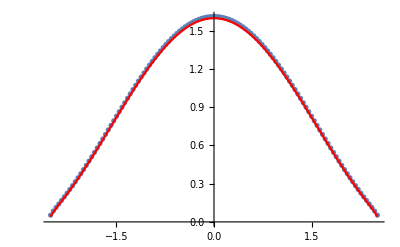

```mathematica
Show[ListPlot[ Transpose[{thets,dn}]],ListPlot[Transpose[{thets ,dnref}],PlotStyle->Red,Joined->True]]
```

```mathematica
relerrDn=(Abs[(dn -dnref)/dnref]);
relerrDs=(Abs[(ds -dsref)/dsref]);
abserrDs=Abs[(ds -dsref)];
abserrDn=Abs[(dn-dnref)];
```

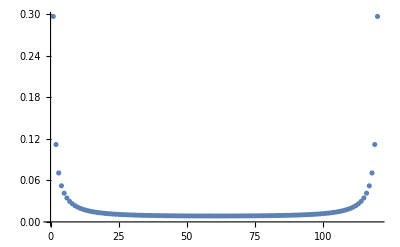

```mathematica
ListPlot[relerrDn,PlotRange->All]
```

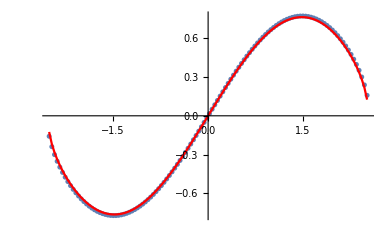

```mathematica
Show[ListPlot[ Transpose[{thets,ds}]],ListPlot[Transpose[{thets ,dsref}],PlotStyle->Red,Joined->True]]
```

```mathematica
hx=Norm[vertex[[2]]-vertex[[1]]]; 
relK1=Abs[1-(dn[[1]]/(√(32./π) (1/Ep)  (2./3)(hx)^(1/2)))/KIref[α]]
relK2=Abs[1-(Abs[ds[[1]]]/(√(32./π) (1/Ep)   (2./3) (hx)^(1/2)))/KIIref[α]]
```

0.432229

0.349281

```mathematica
hx
```

0.0421757

```mathematica
relerrDn //Median
relerrDs //Median
```

0.00989728

0.0106938